```mathematica
<<SymbolicComputing`
DateString[]
$Version
$SCVersion
```

Mon 29 Jan 2018 10:49:26

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 7

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

MathSymbolica Package

Winners of Wolfram Innovator Award 2017

-Graphics-

### How to Install SymbolicCoputing Package

```mathematica
ToExpression[URLFetch["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]]
```

## 1 Limits and Continuity

## Lab 0: An Introduction to Mathematica

Wolfram 언어 커널 실행 방법

Solve x^2-3x=-2 for x.

Use factors to solve the equation.

```mathematica
Factor[x^2-3x+2]
```

(-2+x) (-1+x)

Use Solve command.

```mathematica
Solve[x^2-3x==-2,x]
```

{{x→1},{x→2}}

Solve x^4-3 x^2=4 for real x.

```mathematica
Solve[x^4-3 x^2==4,x]
```

{{x→-2},{x→-ⅈ},{x→ⅈ},{x→2}}

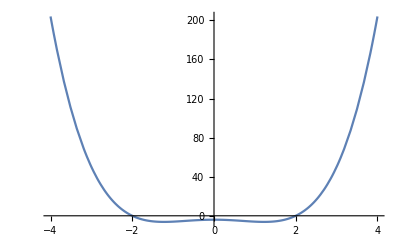

```mathematica
Plot[x^4-3 x^2-4,{x,-4,4}]
```

```mathematica
Solve[x^4-3 x^2==4,x,Reals]
```

{{x→-2},{x→2}}

Find x values of the intersection points of f(x)=14 x^3+2427x-630 and g(x)=781 x^2

```mathematica
Solve[14 x^3+2427x-630==781 x^2,x]
```

{{x→2/7},{x→3},{x→105/2}}

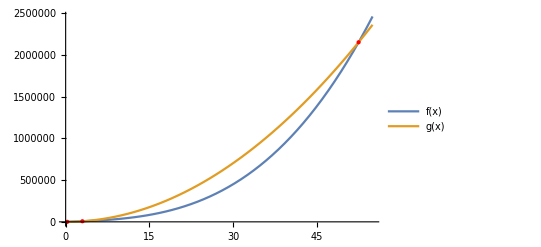

```mathematica
Plot[{14 x^3+2427x-630,781 x^2},{x,0,55},Epilog->{Red,Point[{({x,781 x^2}/.x->2/7),({x,781 x^2}/.x->3),({x,781 x^2}/.x->105/2)}]},PlotLegends->{f[x],g[x]}]
```

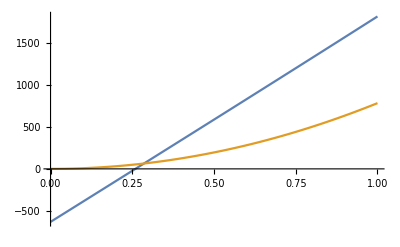
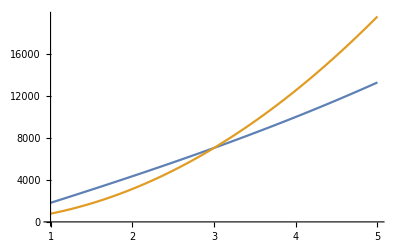
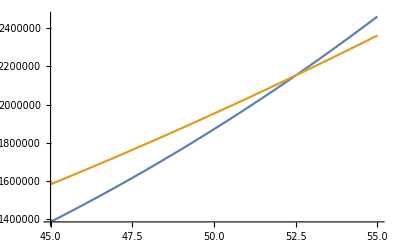

```mathematica
{Plot[#,{x,0,1}],Plot[#,{x,1,5}],Plot[#,{x,45,55}]}&@{14 x^3+2427x-630,781 x^2}
```

Express the above procedure using MathSymbolica package.

```mathematica
<<SymbolicComputing`
```

```mathematica
{f[x]==14 x^3+2427x-630,g[x]==781 x^2}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
SCSolve,{All,x}]
```

{f[x]==-630+2427 x+14 x^3,g[x]==781 x^2}

-630+2427 x+14 x^3==781 x^2

{{x==2/7},{x==3},{x==105/2}}

Find intersection points of f(x)=sin(x) and g(x)=cos(x) for x between 0 and 2π.

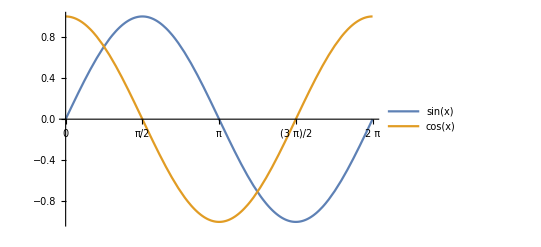

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},Ticks->{{0,π/2,π,3/2 π,2π},Automatic},PlotLegends->"Expressions"]
```

```mathematica
{f[x]==Sin[x],g[x]==Cos[x]}
SCMAF[%,SCEliminate,{All,f[x]==g[x],{f[x],g[x]}},
And,{All,0≤x≤2π},
SCSolve,{All,x},
FullSimplify,{All},Level->{3}]
```

{f[x]==Sin[x],g[x]==Cos[x]}

{{x==-2 ArcTan[1-√2]},{x==2 π-2 ArcTan[1+√2]}}

{{x==π/4},{x==(5 π)/4}}

## Lab 1: Motivating a Need for Limits

Demonstration: Archimedes’ Approximation of Pi

Set the number of sides equal to 3, and calculate the area of inscribed triangle.

Using the fact that the angle of the center is divided into 6 pieces.

```mathematica
S==3 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[30°],"base"->2Sin[30°]}}]
```

S==(3 base height)/2

S==(3 √3)/4

Set the number of sides equal to 6, and calculate the area of inscribed hexagon.

```mathematica
S==6 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[360/12°],"base"->2Sin[360/12°]}}]
```

S==3 base height

S==(3 √3)/2

Determine a general function that will find the area of the inscribed regular n sided polygon.

```mathematica
S==n 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[(2π)/(2n)],"base"->2Sin[(2π)/(2n)]}},
FullSimplify,At[2]]
```

S==(base height n)/2

S==n Cos[π/n] Sin[π/n]

S==n/2 Sin[(2 π)/n]

For n=3,

```mathematica
S==n/2 Sin[(2 π)/n]/.n->3
```

S==(3 √3)/4

For n=6,

```mathematica
S==n/2 Sin[(2 π)/n]/.n->6
```

For n=200,

```mathematica
S==n/2 Sin[(2 π)/n]
SCMAF[%,RA,{At[2],n->200},
N,At[2]]
```

S==n/2 Sin[(2 π)/n]

S==100 Sin[π/100]

S==3.14108

For n→∞,

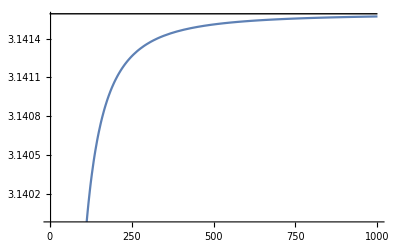

```mathematica
Plot[n/2 Sin[(2 π)/n],{n,3,1000},Epilog->{Style[Line[{{0,π},{1000,π}}],Dotted,Red]}]
```

```mathematica
Limit[n/2 Sin[(2 π)/n],n->∞]
```

π

Or using MathSymbolica,

```mathematica
SCARA[Underscript[Limit, n->∞][S],S==n/2 Sin[(2 π)/n]]
SCMAF[%,SCEvalLimit,At[2]]
```

Limit_(n→∞)[S]==Limit_(n→∞)[n/2 Sin[(2 π)/n]]

Limit_(n→∞)[S]==π

## Lab 2: The Squeeze Theorem

The squeeze theorem states that if f(x)≤g(x)≤h(x) when x is near a (except possibly at a) and lim_(x→a) f(x)=lim_(x→a) h(x)=L then lim_(x→a) g(x)=L.

Demonstration: Squeeze Theorem

```mathematica
Manipulate[Plot[{-Abs[x]^n,x^n Sin[1/x],Abs[x]^n},{x,-.1,.1},
PlotLegends->"Expressions"],{n,{1,2,3}}]
```

Determine lim_(x→0) x sin(1/x).

```mathematica
Simplify[Abs[x]-x Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x Sin[1/x]-(-Abs[x])≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x],-Abs[x]},x->0]
```

{0,0}

Therefore, lim_(x→0) x sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→0) x^2 sin(1/x).

```mathematica
Simplify[Abs[x]^2-x^2 Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x^2 Sin[1/x]-(-Abs[x]^2)≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x]^2,-Abs[x]^2},x->0]
```

{0,0}

Therefore, lim_(x→0) x^2 sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→0) x^3 sin(1/x).

```mathematica
Simplify[Abs[x]^3-x^3 Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x^3 Sin[1/x]-(-Abs[x]^3)≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x]^3,-Abs[x]^3},x->0]
```

{0,0}

Therefore, lim_(x→0) x^3 sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→∞) (sin(x))/x.

```mathematica
Simplify[Abs[1/x]-Sin[x]/x≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[Sin[x]/x-(-Abs[1/x])≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[1/x],-Abs[1/x]},x->∞]
```

{0,0}

Therefore, lim_(x→∞) (sin(x))/x=0 by the squeeze theorem.

Determine lim_(x→∞) (cos(2x))^2/(2x-3).

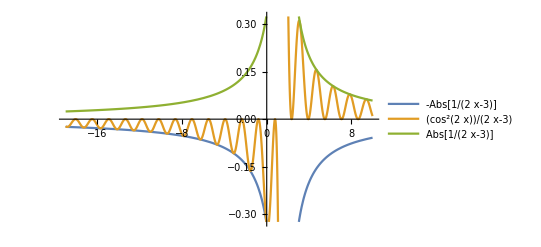

```mathematica
Plot[{-Abs[1/(2x-3)],Cos[2x]^2/(2x-3),Abs[1/(2x-3)]},{x,-19,10},PlotLegends->"Expressions"]
```

```mathematica
Simplify[Abs[1/(2x-3)]-Cos[2x]^2/(2x-3)≥0,Assumptions->{x≠3/2&&x∈Reals}]
```

True

```mathematica
Simplify[Cos[2x]^2/(2x-3)-(-Abs[1/(2x-3)])≥0,Assumptions->{x≠3/2&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[1/(2x-3)],-Abs[1/(2x-3)]},x->∞]
```

{0,0}

Therefore, lim_(x→∞) (cos(2x))^2/(2x-3)=0 by the squeeze theorem.

## Lab 3: Piecing it Together with Limits

Felipe starts at {lat,lon} coordinates {38.8895,-77.0502} and follows the path defined by the function f(x)=-24322.288661448136-632.4272257679265x-4.1045242874237005 x^2. Wade starts at {38.8905,-77.008977} and follows the path defined by w(x)=56.61610495608113+0.2301756594951x.

Locate Felipe and Wade on a map.

```mathematica
GeoGraphics[GeoMarker[{38.8895,-77.0502}],GeoRange->Quantity[.1,"Kilometers"]]
```

-Graphics-

```mathematica
GeoGraphics[GeoMarker[{38.8905,-77.008977}],GeoRange->Quantity[.1,"Kilometers"]]
```

-Graphics-

Determine where Wade and Felipe' s paths will intersect.

```mathematica
f[x_]:=-24322.288661448136-632.4272257679265x-4.1045242874237005 x^2
w[x_]:=56.61610495608113+0.2301756594951x
```

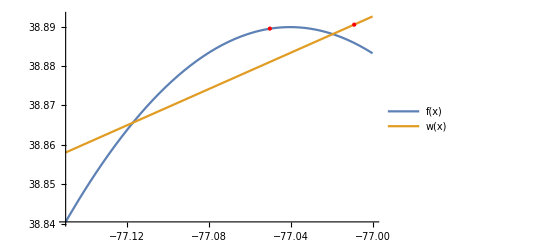

```mathematica
Plot[{f[x],w[x]},{x,-77.15,-77},PlotLegends->"Expressions",Epilog->{PointSize[Medium],Red,Point[Reverse/@{{38.8895,-77.0502},{38.8905,-77.008977}}]}]
```

```mathematica
f[x]==w[x]
SCMAF[%,SCSolve,{All,x,Rule->True}]
```

-24322.3-632.427 x-4.10452 x^2==56.6161+0.230176 x

{{x→-77.1171},{x→-77.0195}}

```mathematica
GeoGraphics[GeoMarker@{f[#],#},GeoRange->Quantity[.3,"Kilometers"]]&[-77.01946127331944]
```

-Graphics-

Using MathSymbolica,

```mathematica
{f[x],x}
SCMAF[%,RA,{All,x==-77.01946127331944},
GeoGraphics[GeoMarker@#,GeoRange->Quantity[.3,"Kilometers"]]&,All]
```

{-24322.3-632.427 x-4.10452 x^2,x}

{38.8881,-77.0195}

-Graphics-

```mathematica
Manipulate[
Module[{f,w},
f[x_]:=-24322.288661448136-632.4272257679265x-4.1045242874237005 x^2;
w[x_]:=56.61610495608113+0.2301756594951x;
Show[
GeoGraphics[{
Tooltip[GeoMarker[{38.8895,-77.0502}],"Felipe's start point"],Tooltip[GeoMarker[{38.8905,-77.008977}],"Wade's start point"],Tooltip[GeoMarker[{f[#],#}]&[-77.01946127331944],"Rendezvous"]}],
GeoListPlot[{
Table[GeoPosition@{f[x],x},{x,-77.0502,-77.0502+0.01 n,0.01}],
Table[GeoPosition@{w[x],x},{x,-77.008977,-77.008977-0.01n,-0.01}]},Joined->True,PlotLegends->{"Felipe's Path","Wade's Path"}]]],
{n,0,4}]
```

Use the Limit command to determine the limit of Felipe and Wade’s path function as x approaches -77.01946127331944.

```mathematica
Limit[f[x],x->-77.01946127331944]
```

38.8881

```mathematica
Limit[w[x],x->-77.01946127331944]
```

38.8881

Define a function h(x) consisting of Felipe and Wade’s actual moving path.

```mathematica
h[x_]:=Piecewise[{{f[x], x≤-77.01946127331944}, {w[x], x>-77.01946127331944}}]
```

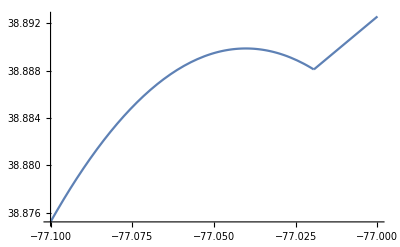

```mathematica
Plot[h[x],{x,-77.1,-77}]
```

Check existence of limit at x=-77.01946127331944.

```mathematica
Limit[h[x],x->-77.01946127331944]
```

Indeterminate

```mathematica
{Limit[h[x],x->-77.01946127331944,Direction->"FromBelow"],Limit[h[x],x->-77.01946127331944,Direction->"FromAbove"]}
%//NumberForm[#,20]&
```

{38.8881,38.8881}

{38.88809966353437,38.88809966353751}

Perform above calculation with exact numbers.

```mathematica
f[x_]:=-24322288661448136*^-12-6324272257679265*^-13x-41045242874237005*^-16 x^2
w[x_]:=5661610495608113*^-14+2301756594951*^-13x
f[x]==w[x]
SCMAF[%,SCSolve,{All,x,Rule->True}]
```

-3040286082681017/125000000000-(1264854451535853 x)/2000000000000-(8209048574847401 x^2)/2000000000000000==5661610495608113/100000000000000+(2301756594951 x)/10000000000000

{{x→(2 (-316328700713710800-√40180728894581018819726550435))/8209048574847401},{x→(2 (-316328700713710800+√40180728894581018819726550435))/8209048574847401}}

```mathematica
Limit[f[x],x->(2 (-316328700713710800+√40180728894581018819726550435))/8209048574847401]==Limit[w[x],x->(2 (-316328700713710800+√40180728894581018819726550435))/8209048574847401]
```

True

A function, f(x), is continuous at a point x=a if
(1) f(a) exists.
(2) lim_(x→a) f(x) exists
(3) f(a)=lim_(x→a) f(x).

```mathematica
f[x_]=.
w[x_]=.
h[x_]=.
```

## Lab 4: Applying the Intermediate Value Theorem

The Intermediate Value Theorem states that if a function f(x) is continuous on the closed interval [a,b] and f(a)<c<f(b) then ∃x∈ [a,b] s.t. f(x)=c.

Exercises:

Estimate the root of a function, f(x)=7 x^3-22 x^2-35x+110, using the Bisection Method with the Intermediate Value Theorem.

a, b. Plot f(x) and determine the number of root.s

f[x]==110-35 x-22 x^2+7 x^3

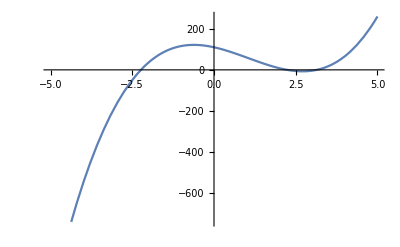

```mathematica
f[x]==7 x^3-22 x^2-35x+110
SCMAF[%,Plot,{At[2],{x,-5,5}},Take->{2}]
```

c. Determine f[3] and f[4].

```mathematica
{f[3],f[4]}/.f[x_]->7 x^3-22 x^2-35x+110
```

{-4,66}

```mathematica
SCARA[{f[3],f[4]},f[x_]==7 x^3-22 x^2-35x+110]
SCMAF[%,Thread,All]
```

{f[3],f[4]}=={-4,66}

{f[3]==-4,f[4]==66}

d. Show that the root exists in [3,4] using the Intermediate Value Theorem.

e. Calculate f[3.5] and determine whether the root lies in [3,3.5] or [3.5,4].

```mathematica
f[x]==7 x^3-22 x^2-35x+110/.x->3.5
```

f[3.5]==18.125

f. Generalize this procedure and find the root using FixedPoint.

If we use infinite precision numbers, we can not reach the fixed point.

```mathematica
f[x_]:=7 x^3-22 x^2-35x+110
FixedPoint[If[f[#[[1]]]f[#[[2]]]<0, {#[[1]],(#[[1]]+#[[2]])/2,#[[2]]},{#[[2]],(#[[2]]+#[[3]])/2,#[[3]]}]&,{3,3.5,4}]
f[x_]=.
```

{3.14286,3.14286,3.14286}

Just two-list is enough.

```mathematica
f[x_]:=7 x^3-22 x^2-35x+110
FixedPointList[If[f[#[[1]]]f[(#[[1]]+#[[2]])/2.]<0, {#[[1]],(#[[1]]+#[[2]])/2.},{(#[[1]]+#[[2]])/2.,#[[2]]}]&,{3,4}]
f[x_]=.
```

Verify your solution using Solve.

```mathematica
Solve[7 x^3-22 x^2-35x+110==0&&3<x<4,x]//N
```

{{x→3.14286}}

```mathematica
f[x]==7 x^3-22 x^2-35x+110
SCMAF[%,RA,{At[1],f[x]==0},
And,{All,3<x<4},
SCSolve,{All,x},Apply->N]
```

f[x]==110-35 x-22 x^2+7 x^3

0==110-35 x-22 x^2+7 x^3&&3<x<4

x==3.14286

## Lab 5: Rates of Change

### Introduction

Average velocity is the rate of change of output values over an interval of input values. Instantaneous velocity or velocity is the rate of change of output values at a single input value.

Exercises:

Let the cumulative sales of a new type of tablet  be modeled by
s(x)=0.17(4.2^x) milion units
where x=0 is the beginning of the fiscal year. Note that the units of x are in years.

a. Find the slope of the line that passes through the function, s(x) for tablet sales through x=0 and x=2.

s==0.17 4.2^x

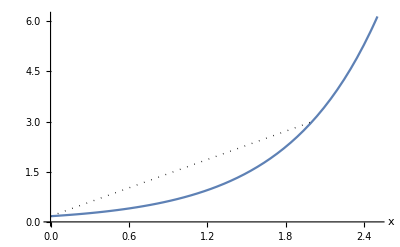

```mathematica
s==0.17 4.2^x
SCMAF[%,Plot,{At[2],{x,0,2.5},Epilog->{Dotted,Line[{{x,0.17 4.2^x}/.x->0,{x,0.17 4.2^x}/.x->2}]},AxesLabel->Automatic},Part->2]
```

```mathematica
m==(s[Subscript[x, 2]]-s[Subscript[x, 1]])/(Subscript[x, 2]-Subscript[x, 1])
SCMAF[%,RA,{At[2],s[x_]==0.17(4.2^x)},
RA,{At[2],{Subscript[x, 1]==0,Subscript[x, 2]==2}}]
```

m==(-s[x_1]+s[x_2])/(-x_1+x_2)

m==(-0.17 4.2^x_1+0.17 4.2^x_2)/(-x_1+x_2)

m==1.4144

b. Determine the units of the slope.

```mathematica
m==(s[Subscript[x, 2]]-s[Subscript[x, 1]])/(Subscript[x, 2]-Subscript[x, 1])
SCMAF[%,RA,{At[2],s[x_]==0.17(4.2^(x/"Years"))"Million Units"},
RA,{At[2],{Subscript[x, 1]==0"Years",Subscript[x, 2]==2"Years"}}]
```

m==(-s[x_1]+s[x_2])/(-x_1+x_2)

m==(-0.17 4.2^(x_1/Years) Million Units+0.17 4.2^(x_2/Years) Million Units)/(-x_1+x_2)

m==(1.4144 Million Units)/Years

c. Determine what the slope we found, represents in terms of rates of change.

m of part a. is an average velocity.

d. Find an equation for the line that passes through s(x) at x=0 and x=2.

without units

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RA,{All,{m==1.4144}},
RR,{All,{Subscript[y, 0]==s[Subscript[x, 1]],Subscript[x, 0]==Subscript[x, 1],s[x_]==0.17(4.2^x),Subscript[x, 1]==0}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

-0.17+y==1.4144 x

y==0.17+1.4144 x

with units.

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RA,{All,{m==(1.4144 "Million Units")/("Years")}},
RR,{All,{Subscript[y, 0]==s[Subscript[x, 1]],Subscript[x, 0]==Subscript[x, 1],s[x_]==0.17(4.2^(x/"Years"))"Million Units",Subscript[x, 1]==0}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

-0.17 Million Units+y==(1.4144 Million Units x)/Years

y==0.17 Million Units+(1.4144 Million Units x)/Years

e. Plot s(x) and the line.

{s[x_]==0.17 4.2^x,y==0.17+1.4144 x}

{0.17 4.2^x,0.17+1.4144 x}

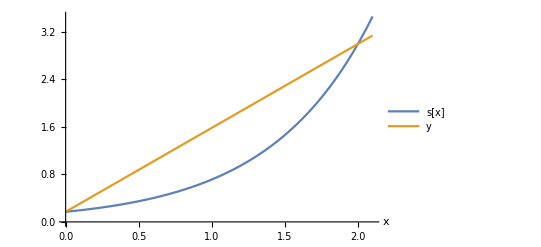

```mathematica
{s[x_]==0.17(4.2^x),y==0.17+1.4144 x}
SCMAF[%,Part,{All,2},Level->{1},
Plot,{All,{x,0,2.1},AxesLabel->Automatic,PlotLegends->{"s[x]","y"}}]
```

f, g. Determine how quickly sales of the tablets are changing exactly at the end of the second year.

```mathematica
Manipulate[Module[{s,sol,y,x},
s[x_]:=0.17(4.2^x);
sol=Solve[y-s[2]==(s[2]-s[x0])/(2-x0)(x-2),y][[1]];
Plot[{s[x],Labeled[y/.sol,(s[2]-s[x0])/(2-x0)]},{x,0,2.1},PlotRange->{0,3.5},PlotLegends->{"s[x]","y"}]
],{x0,0,1.999}]
```

Optimize the manipulate by replacing the Solve expression with a explicit form of line equation.

```mathematica
y-y1==m(x-x1)
SCMAF[%,RA,{At[2],m==(y2-y1)/(x2-x1)},
SCSolve,{All,y}]
```

y-y1==m (x-x1)

y-y1==((x-x1) (-y1+y2))/(-x1+x2)

y==(x y1-x2 y1-x y2+x1 y2)/(x1-x2)

```mathematica
Manipulate[Module[{s,sol,y,x,x1,x2,y1,y2},
s[x_]:=0.17(4.2^x);
y[x_]:=(x y1-x2 y1-x y2+x1 y2)/(x1-x2)/.{x1->2,y1->s[2],x2->x0,y2->s[x0]};
Plot[{s[x],Labeled[y[x],(s[x0]-s[2])/(x0-2)]},{x,1.9,3.1},PlotRange->{2,14},PlotLegends->{"s[x]","y"}]
],{{x0,3},2.001,3}]
```

## Lab 6: Going on Another Tangent

### Introduction

A secant line to a curve is a line that intersects the curve at 2 points. A tangent line to a curve at a given point is a line that just touches the curve at that point.

The slope of the tangent line can be found by

```mathematica
SCARA[Underscript[Limit, x->Subscript[x, 0]][(f[x]-f[Subscript[x, 0]])/(x-Subscript[x, 0])],{(x->Subscript[x, 0])->(h->0),x->Subscript[x, 0]+h},Hold->Subscript[x, 0]]
```

Limit_(x→x_0)[(f[x]-f[x_0])/(x-x_0)]==Limit_(h→0)[(-f[x_0]+f[h+x_0])/h]

### The Derivative of a Function at a Point

Demonstration: The Tangent Line Problem

```mathematica
Manipulate[Module[{y,yp,m,x0=5},
y[x_]:=√x;
m=Limit[(y[x]-y[x0])/(x-x0),x->x0+h];
yp[x_]:=m(x-x0)+y[x0];
Plot[{y[x],yp[x]},{x,0,20},PlotRange->{0,5},
Epilog->{Inset["incline: "<>ToString@N@m],Style[Point@{5,y[5]},PointSize[Medium],Red]}]
]
,{{h,10},0,10}]
```

### Linearization

A tangent line to a function f(x) at x_0 is a very good approximation to f(x) for x values very close to x_0. This idea is called linearization.

Exercises

a. Plot f(x)=x^2-5.

f[x]==-5+x^2

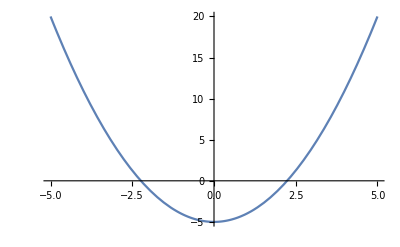

```mathematica
f[x]==x^2-5
SCMAF[%,Plot,{At[2],{x,-5,5}},Take->{2}]
```

b. Find the equation of the tangent line to f(x) at x=2.

```mathematica
m==Underscript[Limit, h->0][(-f[Subscript[x, 0]]+f[h+Subscript[x, 0]])/h]
SCMAF[%,RA,{At[2],f[x_]->x^2-5},Apply->SCEvalLimit,
RA,{All,Subscript[x, 0]->2}]
```

m==Limit_(h→0)[(-f[x_0]+f[h+x_0])/h]

m==2 x_0

m==4

```mathematica
y-Subscript[y, 0]==m(x-Subscript[x, 0])
SCMAF[%,RR,{All,{Subscript[x, 0]->2,Subscript[y, 0]->f[2],m->4}},
RA,{All,{f[x_]==x^2-5,f'[x_]==2 x}},
SCSolve,{All,y}]
```

y-y_0==m (x-x_0)

1+y==4 (-2+x)

y==-9+4 x

{f[x]==-5+x^2,y==-9+4 x}

{f[x],y}=={-5+x^2,-9+4 x}

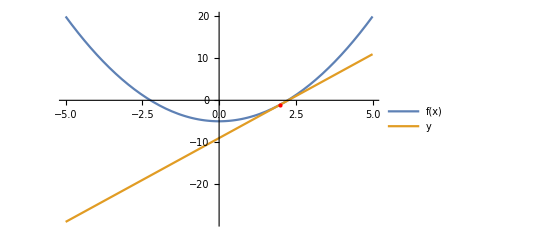

```mathematica
{f[x]==x^2-5,y==-9+4 x}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,-5,5},Epilog->{Red,PointSize[Medium],Point[{{x,x^2-5}/.x->2}]},PlotLegends->At[1]},Take->{2}]
```

c. Find the value of √5 using the tangent line.

```mathematica
y==-9+4 x
SCMAF[%,RA,{All,y==0},
SCSolve,{All,x},Apply->N]
```

y==-9+4 x

0==-9+4 x

x==2.25

Prove lim_(θ→0) (sin θ)/θ=1.

-Graphics-
https://commons.wikimedia.org/wiki/File:Sinx_x _limit _proof.svg

```mathematica
Subscript[S, KOA]≤Subscript[S, KOA]'≤Subscript[S, LOA]
SCMAF[%,RA,{All,{Subscript[S, KOA]==(Cos[θ]Abs[Sin[θ]])/2,Subscript[S, KOA]'==π Abs[θ]/(2π),Subscript[S, LOA]==Abs[Tan[θ]]/2}},
SCMultEq,{All,2/Abs[Sin[θ]]},Apply->SCRecipIneq,
Simplify,{All,Assumptions->{-π/2<θ<π/2}}]
```

S_KOA≤S_KOA'≤S_LOA

(Sec[θ]≤0&&(((|Sin[θ]|)/(|θ|)≤Sec[θ]&&((|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)||(|Sin[θ]|)/(|Tan[θ]|)≥0))||((|Sin[θ]|)/(|θ|)≥0&&0≤(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|))))||(Sec[θ]≥0&&0≤(|Sin[θ]|)/(|θ|)≤Sec[θ]&&0≤(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|))

0≤(|Sin[θ]|)/(|θ|)≤Sec[θ]&&0≤(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)

```mathematica
(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)≤Sec[θ]
SCMAF[%,Underscript[Limit, θ->0],All,Level->{1},
SCEvalLimit,{{At[1]},{At[3]}}]
```

(|Sin[θ]|)/(|Tan[θ]|)≤(|Sin[θ]|)/(|θ|)≤Sec[θ]

Limit_(θ→0)[(|Sin[θ]|)/(|Tan[θ]|)]≤Limit_(θ→0)[(|Sin[θ]|)/(|θ|)]≤Limit_(θ→0)[Sec[θ]]

1≤Limit_(θ→0)[(|Sin[θ]|)/(|θ|)]≤1

Therefore, lim_(θ→0) (sin θ)/θ=1 by the squeeze theorem.

Prove lim_(θ→0) (1-cos θ)/θ.

```mathematica
SCAFE[Underscript[Limit, θ->0][(1-Cos[θ])/θ],SCMultFrac,{All,1+Cos[θ],Apply->Expand}]
SCMAF[%,TrigFactor,{1-Cos[θ]^2},
SCFactor,{θ+θ Cos[θ],θ},
RA,{At[2],Underscript[Limit, θ->0][Sin[θ]^2/(θ (1+Cos[θ]))]==Underscript[Limit, θ->0][Sin[θ]/θ]Underscript[Limit, θ->0][Sin[θ]/(1+Cos[θ])]},
SCEvalLimit,At[2]]
```

Limit_(θ→0)[(1-Cos[θ])/θ]==Limit_(θ→0)[(1-Cos[θ]^2)/(θ+θ Cos[θ])]

Limit_(θ→0)[(1-Cos[θ])/θ]==Limit_(θ→0)[Sin[θ]/θ] Limit_(θ→0)[Sin[θ]/(1+Cos[θ])]

Limit_(θ→0)[(1-Cos[θ])/θ]==0

## Lab 7: Basic Derivative Rules

### Introduction

Derivative notations of Wolfram Language.

```mathematica
{f'[x],f''[x],Derivative[3][f][x]};
```

SymbolicComputing package also provides a fractional form of derivatives.

```mathematica
ⅆf[x]/ⅆx;
```

### Basic Properties of Derivatives

```mathematica
ⅆ/ⅆx x^0
```

0

```mathematica
SCAFE[ⅆc/ⅆx,SCEvalDeriv]
```

ⅆc/ⅆx==0

```mathematica
SCAFE[(ⅆ x^n)/ⅆx,SCEvalDeriv]
```

(ⅆ x^n)/ⅆx==n x^(-1+n)

```mathematica
SCAFE[(ⅆ(c x^n))/ⅆx,SCEvalDeriv]
```

(ⅆ(c x^n))/ⅆx==c n x^(-1+n)

```mathematica
SCAFE[ⅆ/ⅆx(f[x]+g[x]),SCEvalDeriv,Apply->SCAbbrevDeriv]
```

(ⅆ(f[x]+g[x]))/ⅆx==ⅆf/ⅆx+ⅆg/ⅆx

```mathematica
SCAFE[ⅆ/ⅆx(f[x]+g[x]),SCDerivExpand]
```

(ⅆ(f[x]+g[x]))/ⅆx==ⅆf[x]/ⅆx+ⅆg[x]/ⅆx

```mathematica
SCAFE[(ⅆ(c f[x]))/ⅆx,SCDerivExpand]
```

(ⅆ(c f[x]))/ⅆx==c ⅆf[x]/ⅆx

### Derivatives of Trigonometric Functions

```mathematica
ⅆSin[x]/ⅆx==Underscript[Limit, h->0][(Sin[x+h]-Sin[x])/h]
SCMAF[%,TrigExpand,At[2,1],
SCExpandFunc,{At[2],Underscript[Limit, h->0]},Hold->-Sin[x]/h+(Cos[h] Sin[x])/h,
SCFactorFunc,{{At[2,1],Underscript[Limit, h->0],-Cos[x]},{At[2,2],Underscript[Limit, h->0],Sin[x]}},PreApply->Simplify,Apply->Simplify,
SCEvalLimit,At[2]]
```

ⅆSin[x]/ⅆx==Limit_(h→0)[(-Sin[x]+Sin[h+x])/h]

ⅆSin[x]/ⅆx==Sin[x] Limit_(h→0)[(-1+Cos[h])/h]-Cos[x] Limit_(h→0)[-Sin[h]/h]

ⅆSin[x]/ⅆx==Cos[x]

```mathematica
ⅆCos[x]/ⅆx==Underscript[Limit, h->0][(Cos[x+h]-Cos[x])/h]
SCMAF[%,TrigExpand,At[1],Base->Underscript[Limit, h->0][x_],
SCExpandFunc,{At[2],Underscript[Limit, h->0]},Hold->-Cos[x]/h+(Cos[h] Cos[x])/h,
SCFactorFunc,{{At[2,1],Underscript[Limit, h->0],-Cos[x]},{At[2,2],Underscript[Limit, h->0],-Sin[x]}},PreApply->Simplify,
Simplify,At[2],Apply->SCEvalLimit]
```

ⅆCos[x]/ⅆx==Limit_(h→0)[(-Cos[x]+Cos[h+x])/h]

ⅆCos[x]/ⅆx==Limit_(h→0)[-Cos[x]/h+(Cos[h] Cos[x])/h-(Sin[h] Sin[x])/h]

## Lab 8: Derivative Rules (Continued)

### Product Rule

```mathematica
SCAFE[(ⅆ(f[x]g[x]))/ⅆx,SCDerivExpand,Apply->SCAbbrevFunc]
```

(ⅆ(f[x] g[x]))/ⅆx==g ⅆf/ⅆx+f ⅆg/ⅆx

```mathematica
(ⅆ f[x]g[x])/ⅆx==Underscript[Limit, h->0][(f[x+h]g[x+h]-f[x]g[x])/h]
SCMAF[%,Apart,At[2,1],
RA,{At[2],{f[h+x] g[h+x]->f[h+x] g[h+x]-f[h+x] g[x],f[x] g[x]->f[x] g[x]-f[h+x] g[x]}},
Simplify,All,Level->{3},
SCExpandFunc,{At[2],Underscript[Limit, h->0]},Hold->{((-f[x]+f[h+x]) g[x])/h,(f[h+x] (-g[x]+g[h+x]))/h},
SCFactorFunc,{Underscript[Limit, h->0][((-f[x]+f[h+x]) g[x])/h],Underscript[Limit, h->0],g[x]},
RA,{At[2],Underscript[Limit, h->0][(f[h+x] (-g[x]+g[h+x]))/h]==f[x]Underscript[Limit, h->0][(-g[x]+g[h+x])/h]},
RA,{At[2],{Underscript[Limit, h->0][(-f[x]+f[h+x])/h]==ⅆf[x]/ⅆx,Underscript[Limit, h->0][(-g[x]+g[h+x])/h]==ⅆg[x]/ⅆx}}]
```

(ⅆf[x] g[x])/ⅆx==Limit_(h→0)[(-f[x] g[x]+f[h+x] g[h+x])/h]

(ⅆf[x] g[x])/ⅆx==g[x] Limit_(h→0)[(-f[x]+f[h+x])/h]+f[x] Limit_(h→0)[(-g[x]+g[h+x])/h]

(ⅆf[x] g[x])/ⅆx==g[x] ⅆf[x]/ⅆx+f[x] ⅆg[x]/ⅆx

### Quotient Rule

```mathematica
SCAFE[ⅆ/ⅆx f[x]/g[x],SCDerivExpand,All,Apply->SCAbbrevFunc]
```

ⅆ/ⅆx f[x]/g[x]==1/g ⅆf/ⅆx-f/g^2 ⅆg/ⅆx

### Chain Rule

```mathematica
SCAFE[(ⅆ f[g[x]])/ⅆx,SCDerivExpand,All,Apply->SCAbbrevFunc]
```

ⅆf[g[x]]/ⅆx==ⅆf/ⅆg ⅆg/ⅆx